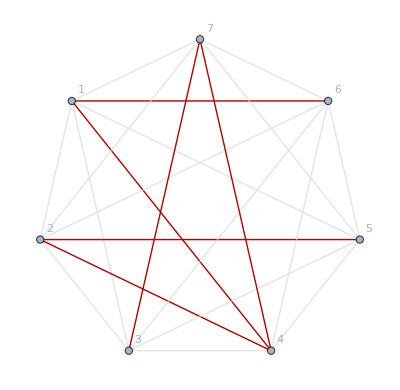

```mathematica
BeautiGraph [ReadGrof[6]]
```

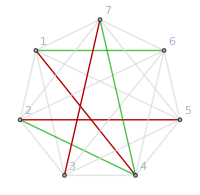
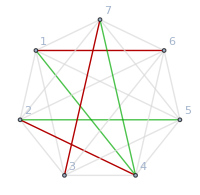
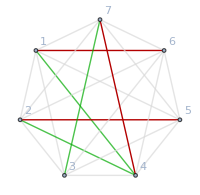
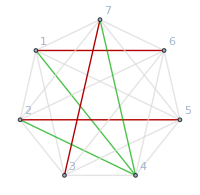

```mathematica
FindB4CReduction[ReadGrof[6]]
```

```mathematica
MakeComplete[v_]:=Map[#[[1]]<->#[[2]]&,Subsets[v,{2}]]
```

```mathematica
MakeComplete[Range[3]]
```

{1<->2,1<->3,2<->3}

```mathematica
BeautiGraph[g_]:=Block[{result,comp=CompleteGraph[VertexCount[g],GraphLayout->"CircularEmbedding"],pos},
pos=First[AbsoluteOptions[comp,VertexCoordinates]][[2]];
Graph[
MakeComplete[VertexList[g]],
GraphHighlight->EdgeList[GraphComplement[g]],
 GraphHighlightStyle->"Thick", 
VertexLabels->"Name", 
EdgeStyle->LightGray,
VertexCoordinates->pos
]
]
```

```mathematica
FindB4CReduction[g_]:=Block[{
Candidates=BarelyFourColorableGraphsOfCount[VertexCount[g]], 
edgeCount=EdgeCount[g], 
difference,
new,
iso,
can2,
result
},
Select[
Flatten[
Table[
difference=EdgeCount[can]-EdgeCount[g];
If[difference==0 ,
If[IsomorphicGraphQ[can,g],
{}<->BeautiGraph[can], Null]
,
Table[
new=EdgeAdd[g,s];
If[IsomorphicGraphQ[new,can],
iso=First[FindGraphIsomorphism [can,new]];
can2=Map[(#[[1]]/.Normal[iso])<->(#[[2]]/.Normal[iso])&,EdgeList[can]];
result=Graph[BeautiGraph[Graph[VertexList[g],can2]],EdgeStyle->Map[#->{Darker[Green],Thick}&,s],ImageSize->200];
result
,
Null
]
,{s,Subsets[EdgeList[GraphComplement[g]],{difference}]}
]
]
,{can,Candidates}
]

],
#=!=Null&
]
]
```

```mathematica
SameEdge[e1_,e2_]:=(e1[[1]]==e2[[1]]&&e1[[2]]==e2[[2]])||(e1[[1]]==e2[[2]]&&e1[[2]]==e2[[1]])
```

```mathematica
ContractReduction[g_,e_]:=Block[{sol=FindB4CReduction[VertexContract[g,{e[[1]],e[[2]]}]],away,env,color,comp=CompleteGraph[VertexCount[g],GraphLayout->"CircularEmbedding"],pos,pos1=Association[],vert},
away=e[[2]];
sol=Map[VertexAdd[#,away]&,sol];
env=EdgeList[g,away<->_];
color=First[Options[sol[[1]],EdgeStyle]][[2]];
color=Join[color,Map[If[SameEdge[e,#] ,#->{Thickness[0.03],Yellow},#->{Thick,Blue}]&,env]];
vert=VertexList[g];
pos=First[AbsoluteOptions[comp,VertexCoordinates]][[2]];
Table[pos1[v]=First[pos];pos=Rest[pos],{v,Sort[vert]}];
pos=Values[pos1];
sol=Map[EdgeAdd[#,env, EdgeStyle->color,VertexCoordinates->pos, VertexLabels->"Name"]&,sol];
sol
]
```

```mathematica
EdgeList[ReadGrof[6]]
```

{1<->2,1<->3,1<->5,1<->7,2<->3,2<->6,2<->7,3<->4,3<->5,3<->6,4<->5,4<->6,5<->6,5<->7,6<->7}

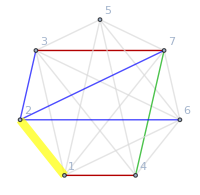
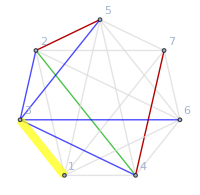
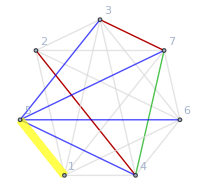
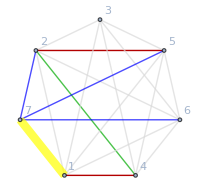
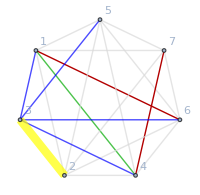
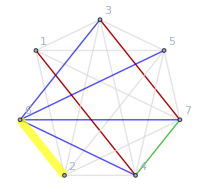
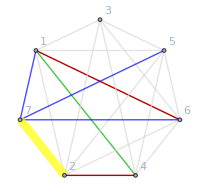
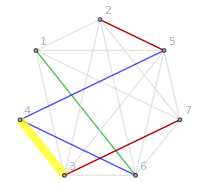
{1<->2<->{-Graphics-},1<->3<->{-Graphics-},1<->5<->{-Graphics-},1<->7<->{-Graphics-},2<->3<->{-Graphics-},2<->6<->{-Graphics-},2<->7<->{-Graphics-},3<->4<->{-Graphics-,-Graphics-,-Graphics-},3<->5<->{-Graphics-,-Graphics-},3<->6<->{-Graphics-,-Graphics-},4<->5<->{-Graphics-,-Graphics-,-Graphics-},4<->6<->{-Graphics-,-Graphics-,-Graphics-},5<->6<->{-Graphics-,-Graphics-},5<->7<->{-Graphics-},6<->7<->{-Graphics-}}

```mathematica
With[{g=ReadGrof[6]},Table[e<->ContractReduction[g,e],{e,EdgeList[g]}]]
```

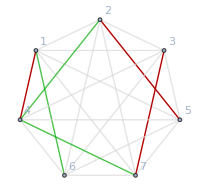
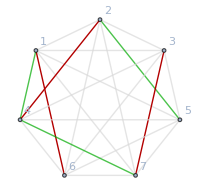
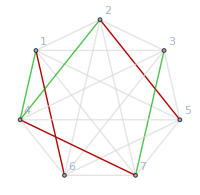
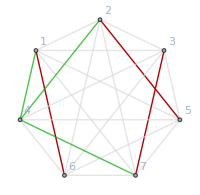

```mathematica
FindB4CReduction[ReadGrof[6]]
```

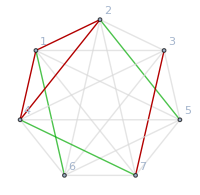
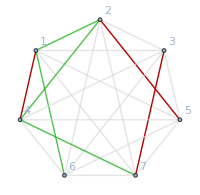
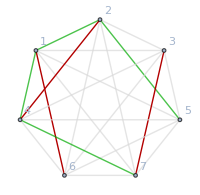
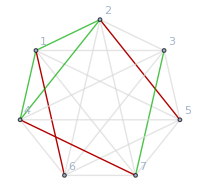
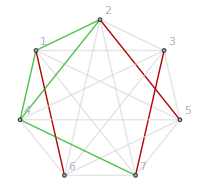
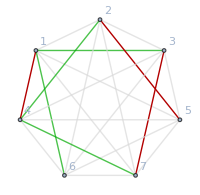
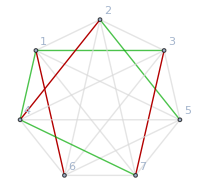
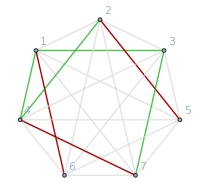
{1<->2<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1<->3<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1<->5<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1<->7<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2<->3<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2<->6<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2<->7<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},3<->4<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},3<->5<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},3<->6<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},4<->5<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},4<->6<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},5<->6<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},5<->7<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},6<->7<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
With[{g=ReadGrof[6]},Table[e<->FindB4CReduction[EdgeDelete[g,e]],{e,EdgeList[g]}]]
```